## Conventional poverty trap

```mathematica
A=10;
α1=Rationalize[0.4];
s1=Rationalize[0.1];
s2=Rationalize[0.2];
s3=10;
d=2;
δP=Rationalize[0.5];
n=Rationalize[0.5];
```

```mathematica
f[kP_]:=A kP^α1;
sf[kP_]:=s1+(s2-s1)/(1+ⅇ^(-s3 (kP-d)));
```

```mathematica
Savings:=sf[kP] f[kP]
Depreciation:=(δP+n) kP
```

Find equilibrium points

```mathematica
kPEq=NSolve[Savings==Depreciation && 0 ≤kP≤4,kP];
```

```mathematica
kPList=kP/.%
```

{0.,1.00008,2.00769,3.17478}

```mathematica
yValues={};
Do[AppendTo[yValues,sf[i] f[i]],{i,kPList}]
```

```mathematica
print[yValues]
```

print[{0.,1.00008,2.00769,3.17478}]

Plot conventional poverty trap

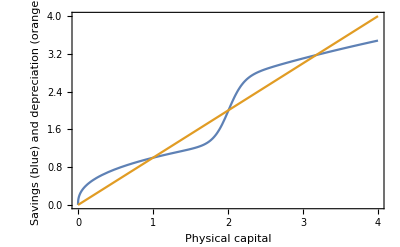

```mathematica
Plot[{Savings,Depreciation}, {kP,0,4}, 
Frame->True, FrameLabel->{"Physical capital", "Savings (blue) and depreciation (orange)"}]
```

## Physical and natural capital

```mathematica
α2 = Rationalize[0.4];
δN = 1;
b=10;
H=Rationalize[1.5];
c1=1;
c2=Rationalize[0.5];
q=Rationalize[0.6];
```

```mathematica
Ef[KN_]:=q KN^α2
G[KN_]:=(b KN^2)/(H^2+KN^2)
L[kP_]:=1/(1+c1 kP^c2)
```

```mathematica
dkPdt:=sf[kP] Ef[KN] f[kP]-(δP+n) kP
dKNdt:=G[KN] L[kP]-δN KN
```

Find equilibrium points

```mathematica
EqPoints=NSolve[{dkPdt==0,dKNdt==0 &&0<=kP≤4&&0<=KN≤5},{kP,KN},Reals,VerifySolutions->True]
```

{{kP→0,KN→0},{kP→0,KN→0.230304},{kP→0.210189,KN→0.345571},{kP→1.13309,KN→4.32345},{kP→2.0161,KN→3.4872},{kP→2.80753,KN→2.98333}}

```mathematica
{dkPdt==0,dKNdt==0 &&0<=kP≤4&&0<=KN≤5}/.%
```

{{True,True},{True,False},{False,False},{True,False},{True,False},{True,True}}

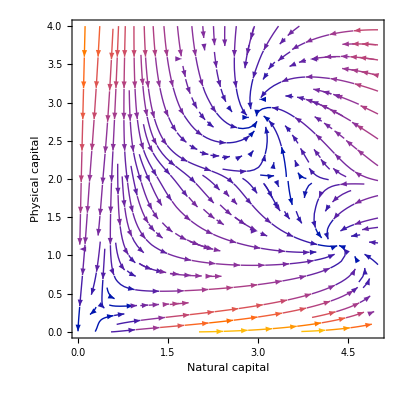

```mathematica
StreamPlot[{dKNdt,dkPdt},{KN,0,5},{kP,0,4}, 
Frame->True, FrameLabel->{"Natural capital", "Physical capital"}]
```

## Physical, natural and cultural capital

```mathematica
T0 =0.35;
P0=2;
PN=2.5;
δC=0.5;
```

```mathematica
P[KN_]=(P0 KN)/(PN+KN);
T[KC_]=T0 KC;
```

```mathematica
dkPdt2:=sf[kP] Ef[KN] f[kP]-(δP+n)kP
dKNdt2:=T[KC] G[KN] L[kP] -δN KN
dKCdt2:=P[KN]-δC KC
```

```mathematica
(* EqPoints=NSolve[{dkPdt==0,dKNdt==0,dKCdt==0 && 0≤kP≤5 && 0≤KN≤5&& 0≤KC≤5},{kP,KN,KC},Reals] *)
```

```mathematica
"CurvesGraphics6`"
```

CurvesGraphics6`

```mathematica
VectorPlot3D[{dKCdt2, dKNdt2,dkPdt2},{KC,0,5},{KN,0,5},{kP,0,5}, 
AxesLabel->{"Cultural  capital", "Natural  capital", "Physical  capital"},
VectorAspectRatio->0.1,
VectorSizes->0.8,
VectorPoints->5]
```

-Graphics3D-

```mathematica
tEnd=24;
kPmin=0;
kPmax=5;
KNmin=0;
KNmax=5;
KCmin=0;
KCmax=5;
stepsize=0.2;
ListIndices={};
Do[AppendTo[ListIndices,{i,j,k}],{i,kPmin,kPmax,stepsize},{j,KNmin,KNmax,stepsize},{k,KCmin,KCmax,stepsize}]
(* Print[ListIndices] *)
ListSol={};
Do[
With[{A=10,α1=0.4,s1=0.1,s2=0.2,s3=10,d=2,δP=0.5,n=0.5,α2 = 0.4,δN = 1,b=10,H=1.5,c1=1,c2=0.5,q=0.6,T0=0.35,P0=2,PN=2.5,δC=0.5},
sol=NDSolveValue[{kP'[t]==(s1+(s2-s1)/(1+ⅇ^(-s3*(kP[t]-d))))*(q*(KN[t])^α2)*(A*(kP[t])^α1)-(δP+n)*kP[t],
KN'[t]==(T0*KC[t])*((b*(KN[t])^2)/(H^2+(KN[t])^2))*(1/(1+c1*(kP[t])^c2))-δN*KN[t],
KC'[t]==((P0*KN[t])/(PN+KN[t]))-δC*KC[t],
kP[0]==i,KN[0]==j,KC[0]==k},{kP[tEnd],KN[tEnd],KC[tEnd]},{t,0,tEnd}];
AppendTo[ListSol,sol]],
{i,kPmin,kPmax,stepsize},{j,KNmin,KNmax,stepsize},{k,KCmin,KCmax,stepsize}]
(* Print[ListSol] *)
AssignClusters=ClusteringComponents[ListSol,3,1];
CountDistinct[AssignClusters]
cluster1={};
Do[If[AssignClusters[[l]]==1,AppendTo[cluster1,ListIndices[[l]]]],{l,1,Length[AssignClusters]}]
(* Print[cluster1]*)
cluster2={};
Do[If[AssignClusters[[m]]==2,AppendTo[cluster2,ListIndices[[m]]]],{m,1,Length[AssignClusters]}]
cluster3={};
Do[If[AssignClusters[[n]]==3,AppendTo[cluster3,ListIndices[[n]]]],{n,1,Length[AssignClusters]}]
ListPointPlot3D[{cluster3,{{1.0,3.4,2.3},{0,0,0}}},
PlotRange->{{kPmin,kPmax},{KNmin,KNmax},{KCmin,KCmax}},
AxesLabel->{"Physical  capital","Natural  capital","Cultural  capital"},
BoxRatios->{1,1,1},
PlotStyle->{Opacity[1],PointSize[0.05]}]
```

3

-Graphics3D-

## Intensification trap model after transformation

```mathematica
ρ=0.5;
L2[kP_]:=ρ+(1-ρ)/(1+c1 kP^c2)
```

```mathematica
dkPdt3:=sf[kP] Ef[KN] f[kP]-(δP+n)kP
dKNdt3:=T[KC] G[KN] L2[kP] -δN KN
dKCdt3:=P[KN]-δC KC
```

```mathematica
VectorPlot3D[{dKCdt3,dkPdt3,dKNdt3},{KC,0,5},{kP,0,5},{KN,0,10}, 
AxesLabel->{"Cultural  capital", "Physical  capital", "Natural  capital"},
BoxRatios->{1, 1, 2},
VectorAspectRatio->0.1,
VectorSizes->0.8,
VectorPoints->{4,4,8}]
```

-Graphics3D-

```mathematica
tEnd=24;
kPmin=0;
kPmax=5;
KNmin=0;
KNmax=10;
KCmin=0;
KCmax=5;
stepsize=0.2;
ListIndices={};
Do[AppendTo[ListIndices,{i,j,k}],{i,kPmin,kPmax,stepsize},{j,KNmin,KNmax,stepsize},{k,KCmin,KCmax,stepsize}]
(* Print[ListIndices] *)
ListSol={};
Do[
With[{A=10,α1=0.4,s1=0.1,s2=0.2,s3=10,d=2,δP=0.5,n=0.5,α2 = 0.4,δN = 1,b=10,H=1.5,c1=1,c2=0.5,q=0.6,T0=0.35,P0=2,PN=2.5,δC=0.5,ρ=0.5},
sol=NDSolveValue[{kP'[t]==(s1+(s2-s1)/(1+ⅇ^(-s3*(kP[t]-d))))*(q*(KN[t])^α2)*(A*(kP[t])^α1)-(δP+n)*kP[t],
KN'[t]==(T0*KC[t])*((b*(KN[t])^2)/(H^2+(KN[t])^2))*(ρ+(1-ρ)/(1+c1*kP[t]^c2))-δN*KN[t],
KC'[t]==((P0*KN[t])/(PN+KN[t]))-δC*KC[t],
kP[0]==i,KN[0]==j,KC[0]==k},{kP[tEnd],KN[tEnd],KC[tEnd]},{t,0,tEnd}];
AppendTo[ListSol,sol]],
{i,kPmin,kPmax,stepsize},{j,KNmin,KNmax,stepsize},{k,KCmin,KCmax,stepsize}]
(* Print[ListSol] *)
AssignClusters=ClusteringComponents[ListSol,Automatic,1];
CountDistinct[AssignClusters]
cluster1={};
Do[If[AssignClusters[[l]]==1,AppendTo[cluster1,ListIndices[[l]]]],{l,1,Length[AssignClusters]}]
(* Print[cluster1] *)
cluster2={};
Do[If[AssignClusters[[m]]==2,AppendTo[cluster2,ListIndices[[m]]]],{m,1,Length[AssignClusters]}]
cluster3={};
Do[If[AssignClusters[[n]]==3,AppendTo[cluster3,ListIndices[[n]]]],{n,1,Length[AssignClusters]}]
ListPointPlot3D[{cluster1,{{0,0,0},{4.6,6.2,2.9}}},
PlotRange->{{kPmin,kPmax},{KNmin,KNmax},{KCmin,KCmax}},
AxesLabel->{"Physical  capital","Natural  capital","Cultural  capital"},
BoxRatios->{1,2,1},
PlotStyle->{Opacity[0.8],PointSize[0.05]}]
```

4

-Graphics3D-

## Subsistence trap model

```mathematica
s=0.2;
A=10;
q=0.6;
α1=0.4;
α2=0.4;
δP=0.5;
n=0.5;
r=0.2;
K=5;
D0=0.8;
D1=4;
D2=2.5;
```

```mathematica
G2[KN_]=r KN (K-KN);
Df[kP_]=D0/(1+ⅇ^(D1 (kP-D2)));
```

```mathematica
dkPdt:=s f[kP] Ef[KN]-(δP+n) kP
dKNdt:=G2[KN]-KN Df[kP]
```

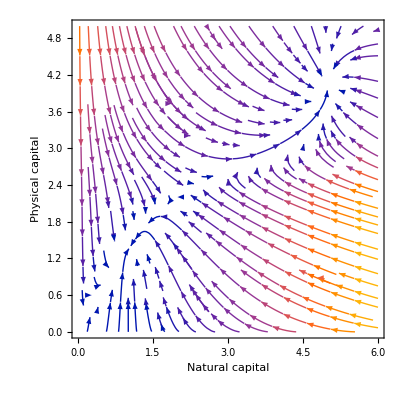

```mathematica
StreamPlot[{dKNdt,dkPdt},{KN,0,6},{kP,0,5}, 
Frame->True, FrameLabel->{"Natural capital", "Physical capital"}]
```